```mathematica
(* Filename: Errors_By_w1_SLE_tuck_A1_2A1_sym_DN
*)
(* Ver. 0 (28-Aug-2025) *)
(*
This file is a program code in Mathematica to get a plot in Fig. 2.
*)
```

```mathematica
nn=127; (* 127 *)
```

```mathematica
(***** In the following line, you need to set a path 
to the folder "For_figs_1_2". *****)
(*
datadir= "D:/.../For_figs_1_2/";
*)
```

```mathematica
mydirC4 = StringJoin[datadir,"/By_w1_SLE_tuck_A1_2A1_sym_DN/dt=1_4/Se16_Tr1000_B256"];
(***)
mydirC8 = StringJoin[datadir,"/By_w1_SLE_tuck_A1_2A1_sym_DN/dt=1_8/Se16_Tr1000_B256"];
(***)
mydirC16= StringJoin[datadir,"/By_w1_SLE_tuck_A1_2A1_sym_DN/dt=1_16/Se16_Tr1000_B256"];
(***)
mydirC32 = StringJoin[datadir,"/By_w1_SLE_tuck_A1_2A1_sym_DN/dt=1_32/Se16_Tr1000_B256"];
(***)
mydirC64 = StringJoin[datadir,"/By_w1_SLE_tuck_A1_2A1_sym_DN/dt=1_64/Se16_Tr1000_B256"];
(***)
mydirA14 = StringJoin[datadir,"/By_w2_revA_SRCK2_avr_Al_DN/dt=1_128/St14_Se16_Tr1000_B256"];
```

```mathematica
fdim=2;
numSetForPrecise=16;
```

```mathematica
numSetForData=16;
```

```mathematica
(* For precise solutions *)
dataMomA14ForEachY=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomA14ForEachY[[ii]]=Table[{},{ii,1,nn}];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirA14<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA14ForEachY[[ii]][[kk]]=locTmp[[kk]];
];
For[iiset = 2,iiset≤numSetForPrecise,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirA14<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomA14ForEachY[[ii]][[kk]]+=locTmp[[kk]];
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomA14ForEachY[[ii]][[kk]]/=numSetForPrecise;

];
];(* End of for ii *)
```

```mathematica
dataMomC4ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomC4ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomC4ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomC4ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomC4ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirC4<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomC4ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirC4<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomC4ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomC4ForEachYAllSet[[ii]][[kk]]=dataMomC4ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomC4ForEachYAllSet[[ii]][[kk]]+=dataMomC4ForEachYEachSet[[ii,kk,iiset]];
];
dataMomC4ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomC8ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomC8ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomC8ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomC8ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomC8ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirC8<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomC8ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirC8<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomC8ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomC8ForEachYAllSet[[ii]][[kk]]=dataMomC8ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomC8ForEachYAllSet[[ii]][[kk]]+=dataMomC8ForEachYEachSet[[ii,kk,iiset]];
];
dataMomC8ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomC16ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomC16ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomC16ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomC16ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomC16ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirC16<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomC16ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirC16<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomC16ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomC16ForEachYAllSet[[ii]][[kk]]=dataMomC16ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomC16ForEachYAllSet[[ii]][[kk]]+=dataMomC16ForEachYEachSet[[ii,kk,iiset]];
];
dataMomC16ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomC32ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomC32ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomC32ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomC32ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomC32ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirC32<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomC32ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirC32<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomC32ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomC32ForEachYAllSet[[ii]][[kk]]=dataMomC32ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomC32ForEachYAllSet[[ii]][[kk]]+=dataMomC32ForEachYEachSet[[ii,kk,iiset]];
];
dataMomC32ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
(***)
dataMomC64ForEachYAllSet=Table[{},{ii,1,fdim}];
dataMomC64ForEachYEachSet=Table[{},{ii,1,fdim}];(**)
For[ii=1, ii≤fdim, ii++,
dataMomC64ForEachYAllSet[[ii]]=Table[{},{ii,1,nn}];
dataMomC64ForEachYEachSet[[ii]]=Table[{},{jj,1,nn}];(**)
For[jj=1,jj<=nn,jj++,
dataMomC64ForEachYEachSet[[ii]][[jj]]=Table[{},{iiset,1,numSetForData}];(**)
];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirC64<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomC64ForEachYEachSet[[ii]][[kk]][[1]]=locTmp[[kk]];(**)
];
For[iiset = 2,iiset≤numSetForData,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirC64<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
dataMomC64ForEachYEachSet[[ii]][[kk]][[iiset]]=locTmp[[kk]];(**)
];
]; (* End of for iiset *)
For[kk=1,kk<=nn,kk++,
dataMomC64ForEachYAllSet[[ii]][[kk]]=dataMomC64ForEachYEachSet[[ii,kk,1]];
For[iiset=2,iiset<=numSetForData,iiset++,
dataMomC64ForEachYAllSet[[ii]][[kk]]+=dataMomC64ForEachYEachSet[[ii,kk,iiset]];
];
dataMomC64ForEachYAllSet[[ii]][[kk]]/=numSetForData;
];
];(* End of for ii *)
```

```mathematica
preciseMomForEachY=dataMomA14ForEachY;
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomC4=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomC4ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomC4[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomC8=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomC8ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomC8[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomC16=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomC16ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomC16[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomC32=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomC32ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomC32[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
(***)
tmpSqErrorForEachY=Table[{},{ii,1,fdim}];
errorMomC64=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachY[[ii]]=Table[{},{ii,1,nn}];
For[kk=1,kk<=nn,kk++,
tmpSqErrorForEachY[[ii]][[kk]]=Total[(dataMomC64ForEachYAllSet[[ii]][[kk]]-preciseMomForEachY[[ii]][[kk]])^2];
];
errorMomC64[[ii]]=Sqrt[Total[tmpSqErrorForEachY[[ii]]]];
];
```

```mathematica
difflistMomC=Table[{},{ii,1,fdim}];
tmpMini=Table[{},{ii,1,5}];
For[ii=1, ii≤fdim, ii++,
tmpMini[[1]]={Log[2,1/4],Log[2,errorMomC4[[ii]]]};
tmpMini[[2]]={Log[2,1/8],Log[2,errorMomC8[[ii]]]};
tmpMini[[3]]={Log[2,1/16],Log[2,errorMomC16[[ii]]]};
tmpMini[[4]]={Log[2,1/32],Log[2,errorMomC32[[ii]]]};
tmpMini[[5]]={Log[2,1/64],Log[2,errorMomC64[[ii]]]};
difflistMomC[[ii]]=Table[tmpMini[[ii]],{ii,1,5}];
];
```

```mathematica
plotlistMomC=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotlistMomC[[ii]]=ListPlot[difflistMomC[[ii]],Joined->True,PlotStyle->DotDashed(*,PlotStyle->Dashing[{0.075,0.05}]*)(*,PlotStyle->PointSize[0.02]*)];
];
```

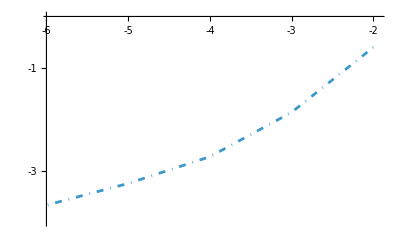

```mathematica
ll=0.015;
ii=1;
Show[plotlistMomC[[ii]],PlotRange->{{-6+0.05,-2+0.05},{-4,0}},AxesOrigin->{-6,0},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,2,6}],Table[{-1ii,ToString[-1ii],ll},{ii,-3,6}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```

```mathematica
numSubSetForData=8;(* 1, 2, 4, 8, 16 *)
numMiniSet=numSetForData/numSubSetForData;
(***)
dataMomC4ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomC4ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomC4ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
(*
If[(1==ii)&&(2>=kk),
Print["(ii=",ii,", kk=",kk,"); ","tmpSt=",tmpSt,", tmpEnd=",tmpEnd];
];
*)
dataMomC4ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomC4ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomC4ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomC4ForEachYEachSet[[ii,kk,iiset]];
];
dataMomC4ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomC8ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomC8ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomC8ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomC8ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomC8ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomC8ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomC8ForEachYEachSet[[ii,kk,iiset]];
];
dataMomC8ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomC16ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomC16ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomC16ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomC16ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomC16ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomC16ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomC16ForEachYEachSet[[ii,kk,iiset]];
];
dataMomC16ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomC32ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomC32ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomC32ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomC32ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomC32ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomC32ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomC32ForEachYEachSet[[ii,kk,iiset]];
];
dataMomC32ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
(***)
dataMomC64ForEachYSubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataMomC64ForEachYSubSet[[ii]]=Table[{},{ii,1,nn}];
For[jj=1,jj<=nn,jj++,
dataMomC64ForEachYSubSet[[ii]][[jj]]=Table[{},{iiset,1,numSubSetForData}];(**)
];
For[kk=1,kk<=nn,kk++,
tmpSt=1;
tmpEnd=tmpSt-1+numMiniSet;
For[ll=1,ll<=numSubSetForData,ll++,
dataMomC64ForEachYSubSet[[ii]][[kk]][[ll]]=dataMomC64ForEachYEachSet[[ii,kk,tmpSt]];
For[iiset=tmpSt+1,iiset<=tmpEnd,iiset++,
dataMomC64ForEachYSubSet[[ii]][[kk]][[ll]]+=dataMomC64ForEachYEachSet[[ii,kk,iiset]];
];
dataMomC64ForEachYSubSet[[ii]][[kk]][[ll]]/=numMiniSet;
tmpSt+=numMiniSet;
tmpEnd=tmpSt-1+numMiniSet;
];
];
];(* End of for ii *)
```

```mathematica
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomC4SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomC4SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomC4ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomC4ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomC4SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomC8SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomC8SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomC8ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomC8ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomC8SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomC16SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomC16SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomC16ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomC16ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomC16SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomC32SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomC32SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomC32ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomC32ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomC32SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
(***)
tmpSqErrorForEachYSubSet=Table[{},{ii,1,fdim}];
errorMomC64SubSet=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpSqErrorForEachYSubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
errorMomC64SubSet[[ii]]=Table[{},{iiset,1,numSubSetForData}];
For[jj=1,jj<=numSubSetForData,jj++,
tmpSqErrorForEachYSubSet[[ii]][[jj]]=Table[{},{ii,1,nn}];
];

For[kk=1,kk<=numSubSetForData,kk++,
For[ll=1,ll<=nn,ll++,
tmpSqErrorForEachYSubSet[[ii]][[kk]][[ll]]=Total[(dataMomC64ForEachYSubSet[[ii]][[ll]][[kk]]-preciseMomForEachY[[ii]][[ll]])^2];
(* Note the order of indexes in dataMomC64ForEachYSubSet, ii,ll,kk, not ii,kk,ll *)
];
];
For[kk=1,kk<=numSubSetForData,kk++,
errorMomC64SubSet[[ii]][[kk]]=Sqrt[Total[tmpSqErrorForEachYSubSet[[ii]][[kk]]]];
];
];
```

```mathematica
errorMomC4Ave=Table[{},{ii,1,fdim}];
errorMomC4Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomC4SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomC4Ave[[ii]]=Mean[tmpErrorList];
errorMomC4Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomC4Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomC8Ave=Table[{},{ii,1,fdim}];
errorMomC8Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomC8SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomC8Ave[[ii]]=Mean[tmpErrorList];
errorMomC8Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomC8Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomC16Ave=Table[{},{ii,1,fdim}];
errorMomC16Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomC16SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomC16Ave[[ii]]=Mean[tmpErrorList];
errorMomC16Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomC16Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomC32Ave=Table[{},{ii,1,fdim}];
errorMomC32Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomC32SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomC32Ave[[ii]]=Mean[tmpErrorList];
errorMomC32Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomC32Ave[[ii]])^2]/numSubSetForData];
];
(***)
errorMomC64Ave=Table[{},{ii,1,fdim}];
errorMomC64Std=Table[{},{ii,1,fdim}];
For[ii=1,ii<=fdim,ii++,
tmpErrorList=Table[errorMomC64SubSet[[ii]][[kk]],{kk,1,numSubSetForData}];
errorMomC64Ave[[ii]]=Mean[tmpErrorList];
errorMomC64Std[[ii]]=Sqrt[Total[(tmpErrorList-errorMomC64Ave[[ii]])^2]/numSubSetForData];
];
```

```mathematica
difflistMomCForAve=Table[{},{ii,1,fdim}];
tmpMini=Table[{},{ii,1,5}];
For[ii=1, ii≤fdim, ii++,
tmpMini[[1]]={Log[2,1/4],Log[2,errorMomC4Ave[[ii]]]};
tmpMini[[2]]={Log[2,1/8],Log[2,errorMomC8Ave[[ii]]]};
tmpMini[[3]]={Log[2,1/16],Log[2,errorMomC16Ave[[ii]]]};
tmpMini[[4]]={Log[2,1/32],Log[2,errorMomC32Ave[[ii]]]};
tmpMini[[5]]={Log[2,1/64],Log[2,errorMomC64Ave[[ii]]]};
difflistMomCForAve[[ii]]=Table[tmpMini[[ii]],{ii,1,5}];
];
```

```mathematica
plotlistMomCForAve=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotlistMomCForAve[[ii]]=ListPlot[difflistMomCForAve[[ii]],Joined->True,PlotStyle->DotDashed(*,PlotStyle->Dashing[{0.075,0.05}]*)(*,PlotStyle->PointSize[0.02]*)];
];
```

```mathematica
plotMiniBarC4ForMom=Table[{},{ii,1,fdim}];
plotMiniBarC8ForMom=Table[{},{ii,1,fdim}];
plotMiniBarC16ForMom=Table[{},{ii,1,fdim}];
plotMiniBarC32ForMom=Table[{},{ii,1,fdim}];
plotMiniBarC64ForMom=Table[{},{ii,1,fdim}];
(***)
For[ii=1, ii≤fdim, ii++,
tmpStep=1/4;
plotMiniBarC4ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomC4Ave[[ii]]+errorMomC4Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomC4Ave[[ii]]-errorMomC4Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarC8ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomC8Ave[[ii]]+errorMomC8Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomC8Ave[[ii]]-errorMomC8Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarC16ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomC16Ave[[ii]]+errorMomC16Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomC16Ave[[ii]]-errorMomC16Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarC32ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomC32Ave[[ii]]+errorMomC32Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomC32Ave[[ii]]-errorMomC32Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
tmpStep/=2;
plotMiniBarC64ForMom[[ii]]=ListPlot[{{Log[2,tmpStep],Log[2,errorMomC64Ave[[ii]]+errorMomC64Std[[ii]]]},{Log[2,tmpStep],Log[2,errorMomC64Ave[[ii]]-errorMomC64Std[[ii]]]}},Joined->True,PlotStyle->Directive[GrayLevel[0.5],AbsoluteThickness[1.5],Opacity[0.66]]];
];
```

```mathematica
tmpUpperListC=Table[{},{ii,1,fdim}];
tmpLowerListC=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
tmpUpperListC[[ii]]={{Log[2,1/4],Log[2,errorMomC4Ave[[ii]]+errorMomC4Std[[ii]]]},{Log[2,1/8],Log[2,errorMomC8Ave[[ii]]+errorMomC8Std[[ii]]]},{Log[2,1/16],Log[2,errorMomC16Ave[[ii]]+errorMomC16Std[[ii]]]},{Log[2,1/32],Log[2,errorMomC32Ave[[ii]]+errorMomC32Std[[ii]]]},{Log[2,1/64],Log[2,errorMomC64Ave[[ii]]+errorMomC64Std[[ii]]]}};
tmpLowerListC[[ii]]={{Log[2,1/4],Log[2,errorMomC4Ave[[ii]]-errorMomC4Std[[ii]]]},{Log[2,1/8],Log[2,errorMomC8Ave[[ii]]-errorMomC8Std[[ii]]]},{Log[2,1/16],Log[2,errorMomC16Ave[[ii]]-errorMomC16Std[[ii]]]},{Log[2,1/32],Log[2,errorMomC32Ave[[ii]]-errorMomC32Std[[ii]]]},{Log[2,1/64],Log[2,errorMomC64Ave[[ii]]-errorMomC64Std[[ii]]]}};
];
```

```mathematica
plotMarkerListCForMom=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotMarkerListCForMom[[ii]]=ListPlot[{tmpUpperListC[[ii]],tmpLowerListC[[ii]]},PlotMarkers->{"",""}(*,PlotMarkers->{"",""}*)];
];
```

numSubSetForData=8

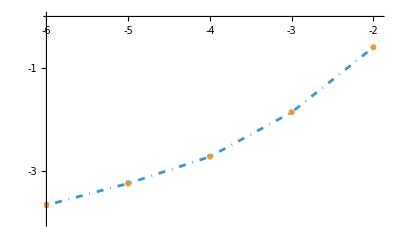

```mathematica
ll=0.03;
Print["numSubSetForData=",numSubSetForData];
ii=1;
Show[plotlistMomCForAve[[ii]],plotMarkerListCForMom[[ii]],plotMiniBarC4ForMom[[ii]],plotMiniBarC8ForMom[[ii]],plotMiniBarC16ForMom[[ii]],plotMiniBarC32ForMom[[ii]],plotMiniBarC64ForMom[[ii]],PlotRange->{{-6+0.05,-2+0.05},{-4,0}},AxesOrigin->{-6,0},Ticks->{Table[{-1ii,ToString[-1ii],ll},{ii,2,6}],Table[{-1ii,ToString[-1ii],ll},{ii,-3,6}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```